## Numeric Solution

```mathematica
g={c,s,i}/.NDSolve[{
c'[t]== c[t](c[t]-a)(1-c[t]) - α c[t] s[t]-β c[t] i[t],
s'[t]== rs s[t](1-s[t])- γ s[t] c[t]+ δ s[t] i[t],
i'[t]== ri i[t]( 1-i[t] )+ η i[t] c[t],
c[0]==1.9227072107386627,s[0]==0.8121091899980447,i[0]==1.484716103547562}/.{
ri ->0.595,
rs ->0.6,
γ ->0.054,
δ ->0.006,
α ->0.15,
β ->0.14,
a ->2.28,
η ->0.15},
{c,s,i},{t,0,20}][[1]];
```

## Plots solutions along each axis

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

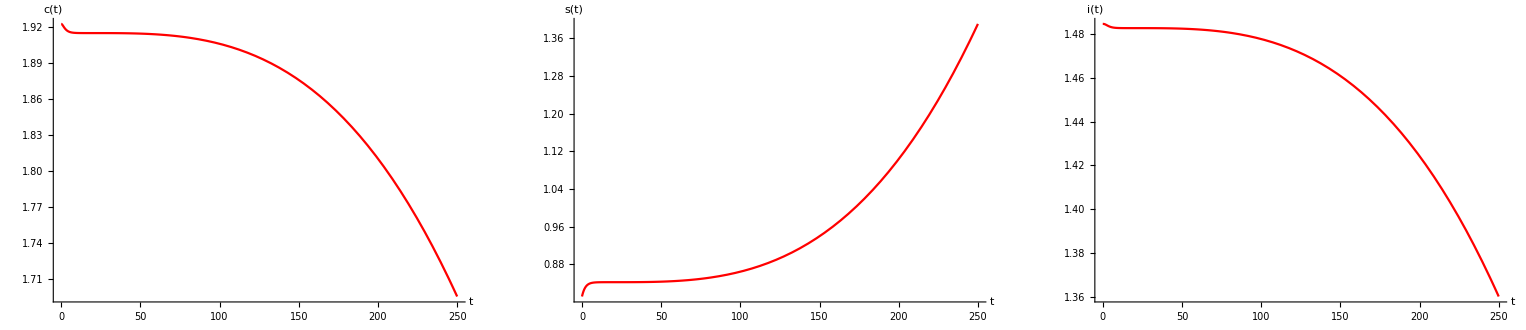

```mathematica
l={c[t],s[t],i[t]};
Show[GraphicsArray[Table[Plot[g[[j]][t],{t,0,250},
PlotRange->All,
PlotStyle->Red,
AxesLabel->TraditionalForm/@{t,l[[j]]},DisplayFunction->Identity],{j,3}]]]
```

## Attractor plot

```mathematica
sol=NDSolve[{
c'[t]== c[t](c[t]-a)(1-c[t]) - α c[t] s[t]-β c[t] i[t],
s'[t]== rs s[t](1-s[t])- γ s[t] c[t]+ δ s[t] i[t],
i'[t]== ri i[t]( 1-i[t] )+ η i[t] c[t],
c[0]==1.9227072107386627,s[0]==0.8121091899980447,i[0]==1.484716103547562}/.{
ri ->0.595,
rs ->0.6,
γ ->0.054,
δ ->0.006,
α ->0.15,
β ->0.14,
a ->2.28,
η ->0.15},
{c,s,i},
{t,0,250},
MaxSteps->∞];
```

```mathematica
ParametricPlot3D[Evaluate[{c[t],s[t],i[t]}/.sol],
{t,0,250},
PlotPoints->1000,
PlotRange->All,
AxesLabel->{"Cancer","Sanas","Inmunes"},
BoxRatios->{1,1,1},
PlotStyle->Directive[Thick,RGBColor[.8,0,0]],
ColorFunction->(ColorData["SolarColors",#4]&)]
```

-Graphics3D-

```mathematica
F11[s_,i_, α_, β_, η_, a_,ri_]:=-s α-i β+(((-1+i) ri-η) (ri-i ri+a η))/η^2
```

```mathematica
(* Inestabilidad oscilatoria *)
```

```mathematica
(*ri ->0.3,
rs ->0.126,
γ ->0.166,
δ ->0.254,
α ->0.32,
β ->0.97,
a ->1.04,
η ->3.3},*)
```

```mathematica
(*ri ->0.264,
rs ->0.6,
γ ->0.21,
δ ->0.006,
α ->0.15,
β ->0.14,
a ->3.21,
η ->0.15},*)
```